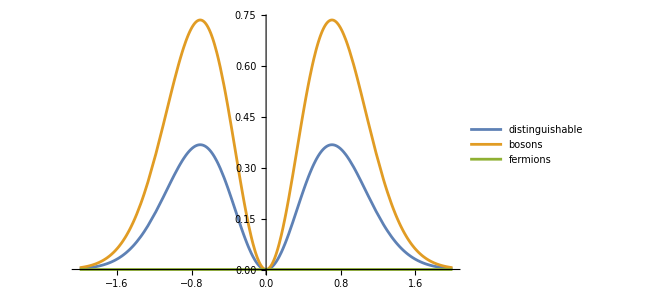

C:\Users\Hanbang Lu\Desktop\PHYS472\assign2\atSamePosition.pdf

```mathematica
atSamePosition = Plot[{2 ξ^2 Exp[-2 ξ^2],4 ξ^2 Exp[-2 ξ^2],0},{ξ,-2,2},PlotLegends->Placed[{"distinguishable","bosons","fermions"},{0.89,0.75}]]
Export["C:\\Users\\Hanbang Lu\\Desktop\\PHYS472\\assign2\\atSamePosition.pdf", atSamePosition]
```

```mathematica
plot1=Plot3D[4 xi2^2 Exp[-xi1^2/2-xi2^2/2],{xi1,-3,3},{xi2,-3,3}, AxesLabel->{Subscript[ξ,1],Subscript[ξ,2],Superscript[Abs[Subscript[ψ,Row[{"(",Subscript[ξ,1],", ",Subscript[ξ,2],")"}]]],2]
},PlotStyle->Opacity[0.5],Mesh->None,PlotRange->All];

plot2=Plot3D[4 xi2^2 Exp[-xi1^2/2-xi2^2/2] (xi1+xi2)^2,{xi1,-3,3},{xi2,-3,3},PlotStyle->{Opacity[0.5],Red},Mesh->None,PlotRange->All];

plot3=Plot3D[4 xi2^2 Exp[-xi1^2/2-xi2^2/2] (xi1-xi2)^2,{xi1,-3,3},{xi2,-3,3},PlotStyle->{Opacity[0.5],Blue},Mesh->None,PlotRange->All];

atDifferentPosition = Show[Legended[plot1,Placed[Style["distinguishable",FontColor->Orange],{0.15,0.8}]],Legended[plot2,Placed[Style["bosons",FontColor->Red],{0.15,0.8}]],Legended[plot3,Placed[Style["fermions",FontColor->Blue],{0.15,0.8}]],
ViewPoint->{0,0,Infinity}]
```

-Graphics-

```mathematica
plot1=Plot3D[4 xi2^2 Exp[-xi1^2/2-xi2^2/2],{xi1,-3,3},{xi2,-3,3}, AxesLabel->{Subscript[ξ,1],Subscript[ξ,2],Superscript[Abs[Subscript[ψ,Row[{"(",Subscript[ξ,1],", ",Subscript[ξ,2],")"}]]],2]
},PlotStyle->Opacity[1],Mesh->None,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["Rainbow"][z]],ColorFunctionScaling->True,Mesh->None,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
plot2=Plot3D[4 xi2^2 Exp[-xi1^2/2-xi2^2/2] (xi1+xi2)^2,{xi1,-3,3},{xi2,-3,3}, AxesLabel->{Subscript[ξ,1],Subscript[ξ,2],Superscript[Abs[Subscript[ψ,Row[{"(",Subscript[ξ,1],", ",Subscript[ξ,2],")"}]]],2]
},PlotStyle->{Opacity[1],Red},Mesh->None,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["Rainbow"][z]],ColorFunctionScaling->True,Mesh->None,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
plot3=Plot3D[4 xi2^2 Exp[-xi1^2/2-xi2^2/2] (xi1-xi2)^2,{xi1,-3,3},{xi2,-3,3}, AxesLabel->{Subscript[ξ,1],Subscript[ξ,2],Superscript[Abs[Subscript[ψ,Row[{"(",Subscript[ξ,1],", ",Subscript[ξ,2],")"}]]],2]
},PlotStyle->{Opacity[1],Blue},Mesh->None,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["Rainbow"][z]],ColorFunctionScaling->True,Mesh->None,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-